# Moving point heat source

In this short notice we explore solution to moving heat source given by the paper “Solutions for modelling moving heat sources in semi-infinite medium and applications to laser material processing”
by M.Van Elsen, M.Baelmans, P.Mercelis, J.-P.Kruth  doi:10.1016/j.ijheatmasstransfer.2007.02.044.

Moving point heat source in 3 D semi-inifinite body is described by Carslaw and Jaeger:
k  - conductivity (W/mK)
T0  -  room temperature (K)
Tm - melting temperature (K)
V - scan speed (m/s)
x - coordinate along scanning direction (m)
y -coordinate perpendicular to scanning direction (m)
z - coordinate in depth (m)
P - laser power (W)

Values of thermal parameters for Ti - 6 Al - 4 V:

In the paper by M.Van Elsen the Eq.(5) there is type error it should be:
θ = P_L/(2 π k R(T-T_o))exp(-V(R+x)/2κ)

```mathematica
Tm=1933;
T0=293;
k=6.0;
κ =2.4 10^-6;
```

```mathematica
θ[P_,κ_,V_,x_,y_,z_]:= P/(2 π k √(x^2+y^2+z^2)(Tm-T0)) Exp[-V(√(x^2+y^2+z^2)+x)/(2 κ)];
```

Result for moving point source

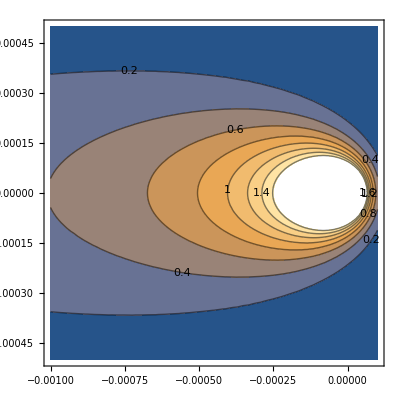

```mathematica
ContourPlot[θ[25.0,κ,0.05,x,y,0.0],{x,-10 10^-4,1 10^-4},{y,-5 10^-4,5 10^-4},ContourLabels->True]
```

These are results for Uniform moving heat source:
The solution is given by M.Van Elsen et al. International Journal of Heat and mass transfer.
50 (2007) 4872-4882.

Definition of the Fourier number:
Fo = (diffusive transport rate)/(storage rate)=αt/L^2

The additional material parameters for uniform source term are:

```mathematica
ρ = 4450; (*density in kg/m^3 *)
cp = 546;(* specific heat in J/kg K *)
k = 6 ; (*conductivity W/m K *)
ah =ch = 0.000075; (* laser dimension in m *)
bh = 0.00005; (* laser dimension in m *)
```

```mathematica
Fos[κ_,s_,t_]:=(κ t)/s^2
```

```mathematica
η [P_,ρ_,cp_,ah_,bh_,ch_,Tm_,To_,t_]:=ρ cp ah bh ch (Tm-To)/(P t);
```

```mathematica
Erfh[κ_,x_,s_,tp_]:=Erf[(√Fos[κ,s,tp])/2(x/s-1)]-Erf[(√Fos[κ,s,tp])/2(x/s+1)]
θunif[P_,κ_,V_,x_,y_,z_,t_]:=-1/(2^5 η[P,ρ,cp,ah,bh,ch,Tm,T0,t])NIntegrate[Erfh[x+V(t-tp),ch,tp]*Erfh[y,ah,tp]*Erfh[z,bh,tp], {tp,0,t}]
```

#### in original paper the Fo is seems defined as s^2/κ(t-t')

```mathematica
mErfh[κ_,x_,s_,t_,tp_]:=Erf[(x-s)/(√(4 κ(t-tp)))]-Erf[(x+s)/(√(4 κ(t-tp)))];
```

```mathematica
mθ[P_,κ_,V_,x_,y_,z_,t_]:=-P/(2^5 ρ ah bh ch (Tm-T0))NIntegrate[mErfh[κ,x+V(t-tp),ch,t,tp] *mErfh[κ,y,ah,t,tp]*mErfh[κ,z,bh,t,tp], {tp,0,t},MinRecursion-> 2]
```

```mathematica
funx[x_,y_,z_,time_]:=-25/(2^5 ρ cp ah bh ch (Tm-T0))NIntegrate[mErfh[κ,x+0.05(time-tp),ch,time,tp]*mErfh[κ,y,ah,time,tp]*mErfh[κ,z,bh,time,tp] ,{tp,0,time},MinRecursion-> 2]
```

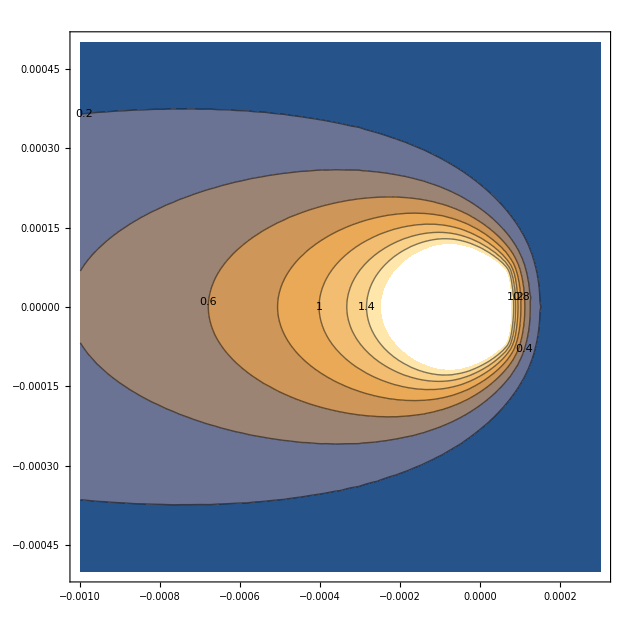

```mathematica
ContourPlot[funx[x,y,0.0,10],{x,-10 10^-4,3 10^-4},{y,-5 10^-4,5 10^-4},ContourLabels->True]
```

3d plot of the uniform moving source:

```mathematica
Plot3D[funx[x,y,0.0,10],{x,-30 10^-4,1 10^-4},{y,-5 10^-4,5 10^-4},PlotRange->{0,3}]
```

-Graphics3D-

Some specific cross sections of this solutions are:

```mathematica
maxRosen=FindMaximum[funx[z,0,0.,10],{z,-1 10^-3}]
```

NIntegrate::inumr: The integrand 4 Erf[(«21»)/(√(«1»))] «1» (Erf[(322.749 (-0.000075+0.05 «1»+z))/(√(10-tp))]-Erf[(«18» («9»+«1»+z))/(√(10+Times[«2»]))]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,2.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{5.03202,{z→-0.0000415872}}

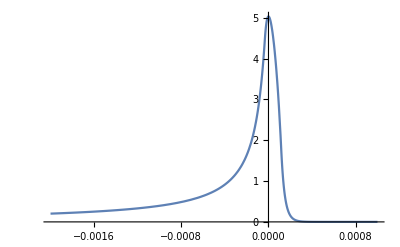

```mathematica
rosen=Plot[funx[x+z/.Last[maxRosen],0,0.0,10],{x,-20 10^-4,10 10^-4}, PlotRange->All]
```

and for x=0 we have:

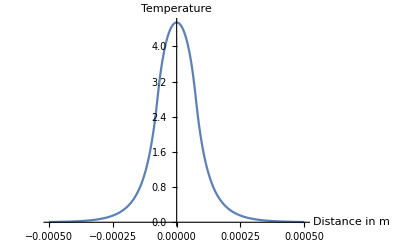

```mathematica
Plot[funx[0,y,0.0,10],{y,-5 10^-4,5 10^-4}, PlotRange->All,AxesLabel->{"Distance in m", "Temperature"}]
```

Read the data obtained numerically:

```mathematica
data=Drop[Drop[Import["C:\\Users\\ivas\\Documents\\Abaqus simulations\\TestCases\\temperature-Ti6Al4V","Table"],4],-5]
```

Import::nffil: File C:\Users\ivas\Documents\Abaqus simulations\TestCases\temperature-Ti6Al4V not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,4].

Drop::drop: Cannot drop positions -5 through -1 in Drop[$Failed,4].

Drop[Drop[$Failed,4],-5]

```mathematica
data[[ Position[data,Max[data]][[1,1]] ,1]]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Drop[Drop[$Failed,4],-5]⟦{{}}⟦1,1⟧,1⟧

```mathematica
fig1=ListPlot[Map[{#[[1]] 10^-3-data[[ Position[data,Max[data]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,data] ]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-5)⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-5)⟦2⟧ is longer than depth of object.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{($Failed)/1000-(Drop[Drop[$Failed,4],-5]⟦{{}}⟦1,1⟧,1⟧)/1000,-289/1640},{((-5)⟦1⟧)/1000-(«1»⟦«1»⟧)/1000,(«1»)/(«4»)}].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-5]⟦{{}}⟦1,1⟧,1⟧,-«44»},{((-5)⟦1⟧)/1000-(«1»)/(«4»),(«1»)/(«4»)}].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-5]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[True,True].

ListPlot::lpn: Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-5]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-5]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-5)⟦1⟧/1000-Drop[Drop[$Failed,4],-5]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-5)⟦2⟧)/1640}]]

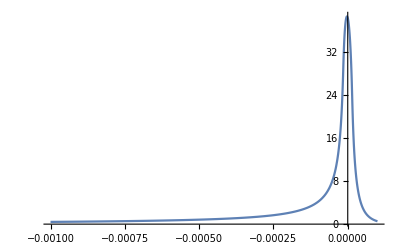
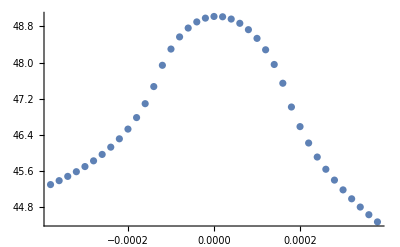
```mathematica
Show[-Graphics-,-Graphics-]
```

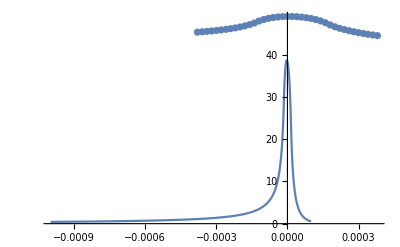

```mathematica
data1=Drop[Drop[Import["C:\\Users\\ivas\\Documents\\Abaqus simulations\\TestCases\\temperature-BC","Table"],3],-4]
```

Import::nffil: File C:\Users\ivas\Documents\Abaqus simulations\TestCases\temperature-BC not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,3].

Drop::drop: Cannot drop positions -4 through -1 in Drop[$Failed,3].

Drop[Drop[$Failed,3],-4]

```mathematica
fig2=ListPlot[Map[{#[[1]] 10^-3-data1[[ Position[data1,Max[data1]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,data1] ]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦2⟧ is longer than depth of object.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{($Failed)/1000-(Drop[Drop[$Failed,3],-4]⟦{{}}⟦1,1⟧,1⟧)/1000,-29/164},{((-4)⟦1⟧)/1000-(«1»⟦«1»⟧)/1000,(«1»)/1640}].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,3],-4]⟦{{}}⟦1,1⟧,1⟧,-«44»},{((-4)⟦1⟧)/1000-(«1»)/(«4»),(«1»)/(«4»)}].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,3],-4]⟦{{}}⟦1,1⟧,1⟧,-0.176829},{(«1»)/1000-«1»,«1»}].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[True,True].

ListPlot::lpn: Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,3],-4]⟦{{}}⟦1,1⟧,1⟧,-0.176829},{(«1»)/1000-«1»,«1»}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,3],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(29/164)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,3],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}]]

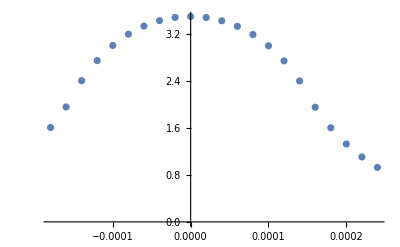
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

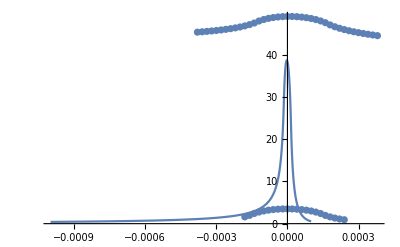

-Graphics-

This is the first comparison with the 75 micron size

```mathematica
data2=Drop[Drop[Import["C:\\Users\\ivas\\Documents\\Abaqus simulations\\TestCases\\temperature-75BC-corr2","Table"],4],-4]
```

Import::nffil: File C:\Users\ivas\Documents\Abaqus simulations\TestCases\temperature-75BC-corr2 not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,4].

Drop::drop: Cannot drop positions -4 through -1 in Drop[$Failed,4].

Drop[Drop[$Failed,4],-4]

```mathematica
Max[data2]
```

Drop[Drop[$Failed,4],-4]

```mathematica
fig3=ListPlot[Map[{#[[1]] 10^-3-data2[[ Position[data2,Max[data2]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,data2]]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦2⟧ is longer than depth of object.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{($Failed)/1000-(Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧)/1000,-289/1640},{((-4)⟦1⟧)/1000-(«1»⟦«1»⟧)/1000,(«1»)/(«4»)}].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-«44»},{((-4)⟦1⟧)/1000-(«1»)/(«4»),(«1»)/(«4»)}].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[True,True].

ListPlot::lpn: Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}]]

```mathematica
dataBCDirchlet = Drop[Drop[Import["C:\\Users\\ivas\\Documents\\Abaqus simulations\\TestCases\\temperature-BC-Dirchlet2xM","Table"],4],-4];
figBCDirchlet=ListPlot[Map[{#[[1]] 10^-3-dataBCDirchlet[[ Position[dataBCDirchlet,Max[dataBCDirchlet]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,dataBCDirchlet],PlotRange->All,PlotStyle->{Orange}]
```

Import::nffil: File C:\Users\ivas\Documents\Abaqus simulations\TestCases\temperature-BC-Dirchlet2xM not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,4].

Drop::drop: Cannot drop positions -4 through -1 in Drop[$Failed,4].

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦2⟧ is longer than depth of object.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{($Failed)/1000-(Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧)/1000,-289/1640},{((-4)⟦1⟧)/1000-(«1»⟦«1»⟧)/1000,(«1»)/(«4»)}].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[True,True].

ListPlot::lpn: Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}],PlotRange→All,PlotStyle→{RGBColor[1, 0.5, 0]}]

```mathematica
dataBCNeumann = Drop[Drop[Import["C:\\Users\\ivas\\Documents\\Abaqus simulations\\TestCases\\temperature-BC-Neumann","Table"],4],-4];
figBCNeumann=ListPlot[Map[{#[[1]] 10^-3-dataBCNeumann[[ Position[dataBCNeumann,Max[dataBCNeumann]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,dataBCNeumann],PlotRange->All,PlotStyle->{Blue}]
```

Import::nffil: File C:\Users\ivas\Documents\Abaqus simulations\TestCases\temperature-BC-Neumann not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,4].

Drop::drop: Cannot drop positions -4 through -1 in Drop[$Failed,4].

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦2⟧ is longer than depth of object.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{($Failed)/1000-(Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧)/1000,-289/1640},{((-4)⟦1⟧)/1000-(«1»⟦«1»⟧)/1000,(«1»)/(«4»)}].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[True,True].

ListPlot::lpn: Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}],PlotRange→All,PlotStyle→{RGBColor[0, 0, 1]}]

```mathematica
dataBCNeumann = Drop[Drop[Import["C:\\Users\\ivas\\Documents\\Abaqus simulations\\TestCases\\temperature-BC-Neumann2xM","Table"],4],-4];
figBCNeumann=ListPlot[Map[{#[[1]] 10^-3-dataBCNeumann[[ Position[dataBCNeumann,Max[dataBCNeumann]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,dataBCNeumann],PlotRange->All,PlotStyle->{Blue}]
```

Import::nffil: File C:\Users\ivas\Documents\Abaqus simulations\TestCases\temperature-BC-Neumann2xM not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,4].

Drop::drop: Cannot drop positions -4 through -1 in Drop[$Failed,4].

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦2⟧ is longer than depth of object.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{($Failed)/1000-(Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧)/1000,-289/1640},{((-4)⟦1⟧)/1000-(«1»⟦«1»⟧)/1000,(«1»)/(«4»)}].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[True,True].

ListPlot::lpn: Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}],PlotRange→All,PlotStyle→{RGBColor[0, 0, 1]}]

```mathematica
dataBCConvection = Drop[Drop[Import["C:\\Users\\ivas\\Documents\\Abaqus simulations\\TestCases\\temperature-BC-Convection2xM","Table"],4],-4];
figBCConvection=ListPlot[Map[{#[[1]] 10^-3-dataBCConvection[[ Position[dataBCConvection,Max[dataBCConvection]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,dataBCConvection],PlotRange->All,PlotStyle->{Red}]
```

Import::nffil: File C:\Users\ivas\Documents\Abaqus simulations\TestCases\temperature-BC-Convection2xM not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,4].

Drop::drop: Cannot drop positions -4 through -1 in Drop[$Failed,4].

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦2⟧ is longer than depth of object.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{($Failed)/1000-(Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧)/1000,-289/1640},{((-4)⟦1⟧)/1000-(«1»⟦«1»⟧)/1000,(«1»)/(«4»)}].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[True,True].

ListPlot::lpn: Drop[{0.001 $Failed-0.001 Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧,-0.17622},{(«1»)/1000-«1»,«1»}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}],PlotRange→All,PlotStyle→{RGBColor[1, 0, 0]}]

```mathematica
Show[figBCConvection,figBCDirchlet,figBCNeumann,fig3,rosen]
```

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[«1»],«3»,].

Show[ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}],PlotRange→All,PlotStyle→{RGBColor[1, 0, 0]}],ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}],PlotRange→All,PlotStyle→{RGBColor[1, 0.5, 0]}],ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}],PlotRange→All,PlotStyle→{RGBColor[0, 0, 1]}],ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}]],-Graphics-]

```mathematica
listMap = Map[{#[[1]] 10^-3-dataBCNeumann[[ Position[dataBCNeumann,Max[dataBCNeumann]][[1,1]] ,1]] 10^-3,(#[[2]]-T0)/(Tm-T0)}&,dataBCNeumann];
ListPlot[Map[(funx[#[[1]]+z/.Last[maxRosen],0,0.0,10]-#[[2]])&,listMap]]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::partd: Part specification (-4)⟦2⟧ is longer than depth of object.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{($Failed)/1000-(Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧)/1000,-289/1640},{((-4)⟦1⟧)/1000-(«1»⟦«1»⟧)/1000,(«1»)/(«4»)}].

NIntegrate::inumr: The integrand 4 Erf[(«21»)/(√(10-tp))] Erf[(«21»)/(«1»)] (Erf[(322.749 («1»))/(√(10-tp))]-Erf[(322.749 («1»))/(√(10+Times[«2»]))]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,2.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[289/1640-697.109 NIntegrate[«1»],-697.109 NIntegrate[«1»,{«1»},MinRecursion→2]+«1»].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,False].

ListPlot::lpn: Drop[0.17622-697.109 NIntegrate[«1»],-697.109 «1»+(293-«1»)/1640] is not a list of numbers or pairs of numbers.

ListPlot[Drop[289/1640-697.109 NIntegrate[mErfh[κ,(-0.0000415872+$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000)+0.05 (10-tp),ch,10,tp] mErfh[κ,0,ah,10,tp] mErfh[κ,0.,bh,10,tp],{tp,0,10},MinRecursion→2],-697.109 NIntegrate[mErfh[κ,(-0.0000415872+(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000)+0.05 (10-tp),ch,10,tp] mErfh[κ,0,ah,10,tp] mErfh[κ,0.,bh,10,tp],{tp,0,10},MinRecursion→2]+(293-(-4)⟦2⟧)/1640]]

Compare analytical solution of Rosenthal with Abaqus solution:

```mathematica
error =Abs[Map[((funx[#[[1]]+z/.Last[maxRosen],0,0.0,10]-#[[2]])/funx[#[[1]]+z/.Last[maxRosen],0,0.0,10])&,listMap]];
```

NIntegrate::inumr: The integrand 4 Erf[(«21»)/(√(10-tp))] Erf[(«21»)/(«1»)] (Erf[(322.749 («1»))/(√(10-tp))]-Erf[(322.749 («1»))/(√(10+Times[«2»]))]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,2.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[-(0.00143449 (289/1640-«18» «1»))/NIntegrate[«1» «1» mErfh[κ,0.,bh,10,tp],«1»,«1»],-(«1»)/(«1»)].

```mathematica
ListPlot[error]
```

NIntegrate::inumr: The integrand 4 Erf[(«21»)/(√(10-tp))] Erf[(«21»)/(«1»)] (Erf[(322.749 («1»))/(√(10-tp))]-Erf[(322.749 («1»))/(√(10+Times[«2»]))]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,2.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[-(0.00143449 (289/1640-«18» «1»))/NIntegrate[«1» «1» mErfh[κ,0.,bh,10,tp],«1»,«1»],-(«1»)/(«1»)].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

ListPlot::lpn: Abs[Drop[-(0.00143449 («20»-«18» «1»))/NIntegrate[«1»],-(«22» («1»+«1»))/NIntegrate[«1»]]] is not a list of numbers or pairs of numbers.

ListPlot[Abs[Drop[-((0.00143449 (289/1640-697.109 NIntegrate[mErfh[κ,(-0.0000415872+$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000)+0.05 (10-tp),ch,10,tp] mErfh[κ,0,ah,10,tp] mErfh[κ,0.,bh,10,tp],{tp,0,10},MinRecursion→2]))/NIntegrate[mErfh[κ,(-0.0000415872+$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000)+0.05 (10-tp),ch,10,tp] mErfh[κ,0,ah,10,tp] mErfh[κ,0.,bh,10,tp],{tp,0,10},MinRecursion→2]),-((0.00143449 (-697.109 NIntegrate[mErfh[κ,(-0.0000415872+(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000)+0.05 (10-tp),ch,10,tp] mErfh[κ,0,ah,10,tp] mErfh[κ,0.,bh,10,tp],{tp,0,10},MinRecursion→2]+(293-(-4)⟦2⟧)/1640))/NIntegrate[mErfh[κ,(-0.0000415872+(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000)+0.05 (10-tp),ch,10,tp] mErfh[κ,0,ah,10,tp] mErfh[κ,0.,bh,10,tp],{tp,0,10},MinRecursion→2])]]]

```mathematica
??error
```

```mathematica
Mean@Map[If[# === Indeterminate,0.0,#]&,error]
```

NIntegrate::inumr: The integrand 4 Erf[(«21»)/(√(10-tp))] Erf[(«21»)/(«1»)] (Erf[(322.749 («1»))/(√(10-tp))]-Erf[(322.749 («1»))/(√(10+Times[«2»]))]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,2.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[-(0.00143449 (289/1640-«18» «1»))/NIntegrate[«1» «1» mErfh[κ,0.,bh,10,tp],«1»,«1»],-(«1»)/(«1»)].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Mean[Abs[Drop[-((0.00143449 (289/1640-697.109 NIntegrate[mErfh[κ,(-0.0000415872+$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000)+0.05 (10-tp),ch,10,tp] mErfh[κ,0,ah,10,tp] mErfh[κ,0.,bh,10,tp],{tp,0,10},MinRecursion→2]))/NIntegrate[mErfh[κ,(-0.0000415872+$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000)+0.05 (10-tp),ch,10,tp] mErfh[κ,0,ah,10,tp] mErfh[κ,0.,bh,10,tp],{tp,0,10},MinRecursion→2]),-((0.00143449 (-697.109 NIntegrate[mErfh[κ,(-0.0000415872+(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000)+0.05 (10-tp),ch,10,tp] mErfh[κ,0,ah,10,tp] mErfh[κ,0.,bh,10,tp],{tp,0,10},MinRecursion→2]+(293-(-4)⟦2⟧)/1640))/NIntegrate[mErfh[κ,(-0.0000415872+(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000)+0.05 (10-tp),ch,10,tp] mErfh[κ,0,ah,10,tp] mErfh[κ,0.,bh,10,tp],{tp,0,10},MinRecursion→2])]]]

```mathematica
maxError=Abs@(First[maxRosen]-(Max[dataBCDirchlet]-T0)/(Tm-T0))/First[maxRosen]
```

0.198728 Abs[5.03202+(293-Drop[Drop[$Failed,4],-4])/1640]

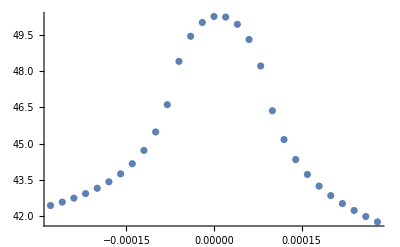
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,fig3]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,ListPlot[Drop[{$Failed/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,-(289/1640)},{(-4)⟦1⟧/1000-Drop[Drop[$Failed,4],-4]⟦{{}}⟦1,1⟧,1⟧/1000,(-293+(-4)⟦2⟧)/1640}]]]

Implementation of the semi-ellipsoidal moving heat source:
The result in dimensional form is given by:
θ/n=1/(√(2π))∫_0^((V^2 t)/(2κ)) 1/(√(τ+u_a^2)√(τ+u_b^2))(A_1/(√(τ+u_c^2)))ⅆτ

Nondimensional variables using Christensen method:

```mathematica
ξ[x_]:=V x /(2 κ);
ψ[y_]:= V y/(2 κ);
ζ[z_]:= V z/(2 κ);
τ[t_]:= V^2 (t-tp)/(2 κ);
ua=V ah 2 √6 κ; uc=V ch 2 √6 κ;
ub=V bh 2 √6 κ; n=P V/(4 π κ^2 ρ cp(Tm-T0));
```

```mathematica
A1[x_,y_,z_,t_] :=Exp[(-(ξ[x]+τ[t])^2)/(2(τ[t]+uc^2))-□/□]
```

This solution of the Rosenthal solution is provided by Erics code:

```mathematica
F[u_]:=1/(u π) Integrate[1-Exp[-2 u/(1+s^2)],{s,0,∞}]
υ[Po_,ω_,v_]:= Po/(k π ω) F[v ω/(2 η)]
```

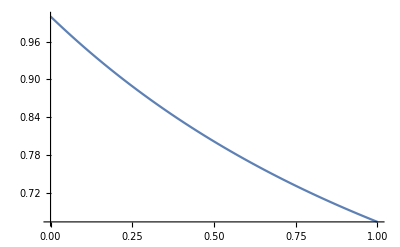

```mathematica
Plot[F[u],{u,0,1}]
```

Material properties used by Eric:

```mathematica
ρ=0.008; cp=0.55; k=0.05; ω=0.2; v=50; Po=66.5;
```

```mathematica
η := k/(ρ cp); δ := 2 η/v;
```

Temperature at origin is given by:

```mathematica
υ[Po,ω,v]//N
```

1737.29